### Start choosing the example:

```mathematica
t=11;
beta = 0;
A = 0.2;
g[x]
```

Log[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}}|>

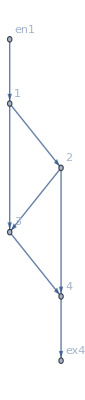

```mathematica
d2e["FG"]
```

```mathematica
(rule=CriticalCongestionSolver[d2e=D2E[Data/.{I1->800,U2->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}]])//AbsoluteTiming
```

```mathematica
Select[d2e["RulesCriticalCase"],NumericQ]
```

<|j13→0,j12→800,j14→800,u12→15,jt2→0,jt23→0,jt24→0,jt4→0,u11→15,j11→0|>

```mathematica
(rule=CriticalCongestionSolver[d2e=D2E[Data/.{I1->40,U2->0, S1->0,S2->0,S3->0,S4->0,S5->0,S6->0, S7->100,S8->100,S9->100,S10->100,S11->100,S12->0,S13->0,S14->0,S15->0,S16->0}]])//AbsoluteTiming
```

Variables are all set

Assembled most elements of the system

CleanEqualities for the switching conditions on each vertex

CleanEqualities for the complementary conditions (given the rules)

CleanEqualities for the values at the auxiliary edges

CleanEqualities for the balance conditions in terms of (mostly) transition currents

CleanEqualities for the critical case equations

Expanding critical rules...

EliminateVarsSimplify for the us

(Maybe the) system is not feasible!

            	Check the paper: The current method for stationary mean-field games on networks

<|u1→u1,u2→-40+jt13+jt14-jt15-jt17+u1,u3→u1,u4→-jt13-jt14+jt15+jt17+u1,u5→-40+jt13+jt14-jt15-jt17+u1,u6→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u7→-40+jt13+jt14-jt15-jt17+u1,u8→-80-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1,u9→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u10→-40+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1,u11→0,u12→0,u13→u1,u14→u1|>

<|u11→0,u12→0|>

<|u11→0,u12→0,j1→j1,j2→j2,j3→j3,j4→j4,j5→j5,j6→j6,j7→j7,j8→j8,j9→j9,j10→j10,j11→0,j12→40,j13→0,j14→40|>

<|j2→40+jt1-jt13-jt14+jt15+jt17,j4→jt13+jt14,j13→0,j1→jt1,j6→jt15+jt16,j8→40+jt1+jt10-jt11-jt13-jt14-jt16+jt17+jt21,j3→jt15+jt17,j5→jt1+jt10-jt11,j10→jt14+jt16,j7→jt21,j9→jt1+jt10-jt11-jt13+jt17,j12→40,j14→40,u12→0,u3→u1,u5→-40+jt13+jt14-jt15-jt17+u1,u7→-40+jt13+jt14-jt15-jt17+u1,u9→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,jt2→0,jt23→0,jt24→0,jt4→0,u11→0,u14→u1,j11→0,jt12→-jt11+jt21,jt18→jt1+jt10-jt11-jt13,jt19→jt1+jt10-jt11-jt13+jt17,jt20→40-jt14-jt16+jt21,jt22→jt14+jt16-jt21,jt3→jt15+jt17,jt5→40+jt1-jt13-jt14,jt6→-jt1+jt13+jt14,jt7→jt11+jt15+jt16-jt21,jt8→40+jt1-jt11-jt13-jt14-jt16+jt17+jt21,jt9→jt1-jt11,u10→-40+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1,u2→-40+jt13+jt14-jt15-jt17+u1,u4→-jt13-jt14+jt15+jt17+u1,u6→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u8→-80-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1,u13→u1|>

<|j2→40+jt1-jt13-jt14+jt15+jt17,j4→jt13+jt14,j13→0,j1→jt1,j6→jt15+jt16,j8→40+jt1+jt10-jt11-jt13-jt14-jt16+jt17+jt21,j3→jt15+jt17,j5→jt1+jt10-jt11,j10→jt14+jt16,j7→jt21,j9→jt1+jt10-jt11-jt13+jt17,j12→40,j14→40,u12→0,u3→u1,u5→-40+jt13+jt14-jt15-jt17+u1,u7→-40+jt13+jt14-jt15-jt17+u1,u9→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,jt2→0,jt23→0,jt24→0,jt4→0,u11→0,u14→u1,j11→0,jt12→-jt11+jt21,jt18→jt1+jt10-jt11-jt13,jt19→jt1+jt10-jt11-jt13+jt17,jt20→40-jt14-jt16+jt21,jt22→jt14+jt16-jt21,jt3→jt15+jt17,jt5→40+jt1-jt13-jt14,jt6→-jt1+jt13+jt14,jt7→jt11+jt15+jt16-jt21,jt8→40+jt1-jt11-jt13-jt14-jt16+jt17+jt21,jt9→jt1-jt11,u10→-40+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1,u2→-40+jt13+jt14-jt15-jt17+u1,u4→-jt13-jt14+jt15+jt17+u1,u6→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u8→-80-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1,u13→u1|>

j1≥0&&j2≥0&&j3≥0&&j4≥0&&j5≥0&&j6≥0&&j7≥0&&j8≥0&&j9≥0&&j10≥0&&(j1==0||j2==0)&&(j3==0||j4==0)&&(j5==0||j6==0)&&(j7==0||j8==0)&&(j9==0||j10==0)

Finish with the js

<|u1→u1,u2→-40+jt13+jt14-jt15-jt17+u1,u3→u1,u4→-jt13-jt14+jt15+jt17+u1,u5→-40+jt13+jt14-jt15-jt17+u1,u6→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u7→-40+jt13+jt14-jt15-jt17+u1,u8→-80-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1,u9→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u10→-40+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1,u11→0,u12→0,u13→u1,u14→u1|>

{j1≥0&&40+j1-j2+j3≥0&&-j1+j2+j5-j6+j7≥0&&-40-j1+j10+j2+j5-j6≥0&&(j1==0||j2==0)&&(j3==0||40+j1-j2+j3==0)&&(j7==0||-j1+j2+j5-j6+j7==0)&&(-40-j1+j10+j2+j5-j6==0||j10==0),j2≥0&&40+j1-j2+j3≥0&&-j1+j2+j5-j6+j7≥0&&-40-j1+j10+j2+j5-j6≥0&&(j1==0||j2==0)&&(j3==0||40+j1-j2+j3==0)&&(j7==0||-j1+j2+j5-j6+j7==0)&&(-40-j1+j10+j2+j5-j6==0||j10==0),j3≥0&&40+j1-j2+j3≥0&&(j3==0||40+j1-j2+j3==0),True,j5≥0&&-j1+j2+j5-j6+j7≥0&&-40-j1+j10+j2+j5-j6≥0&&(j5==0||j6==0)&&(j7==0||-j1+j2+j5-j6+j7==0)&&(-40-j1+j10+j2+j5-j6==0||j10==0),j6≥0&&-j1+j2+j5-j6+j7≥0&&-40-j1+j10+j2+j5-j6≥0&&(j5==0||j6==0)&&(j7==0||-j1+j2+j5-j6+j7==0)&&(-40-j1+j10+j2+j5-j6==0||j10==0),j7≥0&&-j1+j2+j5-j6+j7≥0&&(j7==0||-j1+j2+j5-j6+j7==0),True,True,-40-j1+j10+j2+j5-j6≥0&&j10≥0&&(-40-j1+j10+j2+j5-j6==0||j10==0),True,True,True,True}

{(j5<-40+j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(40≤j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)||(-j5+j6<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==-40+j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==40&&j1==0&&j7==0&&j10==-j5+j6&&j3==0)||(40<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(-40+j6<j5<j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(40≤j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40&&j1==0&&((j7==-40-j5+j6&&j10==0&&j3==0)||(j7==0&&j10==0&&j3==0)))||(j2>40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j6<j5<40+j6&&((j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<0&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==0&&((j1==0&&((j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&(j3==-40+j2||j3==0))||(j7==0&&j10==0&&(j3==-40+j2||j3==0))))||(40-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==40+j6&&((j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<0&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==0&&((j1==0&&((j7==-j5+j6&&j10==0&&(j3==-40||j3==0))||(j7==0&&j10==0&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5>40+j6&&((j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&(j3==-40+j2||j3==0))||(j7==0&&j10==0&&(j3==-40+j2||j3==0))))||(40-j5+j6<j2<0&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2==0&&((j1==0&&((j7==-j5+j6&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))||(j7==0&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))))||(0<j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&(j3==-40-j1||j3==0))||(j7==0&&j10==0&&(j3==-40-j1||j3==0))))||(-40+j5-j6<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2))))))),(j5<-40+j6&&((j2==0&&((j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&j3==-40-j1)||(j7==0&&j10==0&&j3==-40-j1)))||(-40+j5-j6<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)||(j5-j6<j1≤-40&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j1>-40&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(40≤j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)||(-j5+j6<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==-40+j6&&((j2==0&&((j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&j3==-40-j1)||(j7==0&&j10==0&&j3==-40-j1)))||(-40+j5-j6<j1<-40&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)))||(j1==-40&&j7==0&&j10==-j5+j6&&j3==0)||(-40<j1<0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==40&&j1==0&&j7==0&&j10==-j5+j6&&j3==0)||(40<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(-40+j6<j5<j6&&((j2==0&&((j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&j3==-40-j1)||(j7==0&&j10==0&&j3==-40-j1)))||(-40+j5-j6<j1≤-40&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)))||(-40<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j5-j6<j1<0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(40≤j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==j6&&((j2==0&&((j1<-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40&&((j7==-40-j5+j6&&j10==0&&j3==0)||(j7==0&&j10==0&&j3==0)))||(-40<j1<0&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==0&&j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40&&j1==0&&((j7==-40-j5+j6&&j10==0&&j3==0)||(j7==0&&j10==0&&j3==0)))||(j2>40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j6<j5<40+j6&&((j2==0&&((j1≤-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(-40<j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&(j3==-40-j1||j3==0))||(j7==0&&j10==0&&(j3==-40-j1||j3==0))))||(-40+j5-j6<j1<0&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==0&&((j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&(j3==-40+j2||j3==0))||(j7==0&&j10==0&&(j3==-40+j2||j3==0))))||(40-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==40+j6&&((j2==0&&((j1≤-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(-40<j1<0&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==0&&((j7==-j5+j6&&j10==0&&(j3==-40||j3==0))||(j7==0&&j10==0&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5>40+j6&&((j2==0&&((j1≤-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(-40<j1<0&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==0&&((j7==-j5+j6&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))||(j7==0&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))))||(0<j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&(j3==-40-j1||j3==0))||(j7==0&&j10==0&&(j3==-40-j1||j3==0))))||(-40+j5-j6<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2))))))),(j1≤-40+j2&&j3==-40-j1+j2)||(j1>-40+j2&&j3==0),True,(j1<-40+j2&&((j6<0&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==0&&((j5==0&&((j7==j1-j2&&(j10==40+j1-j2||j10==0))||(j7==0&&(j10==40+j1-j2||j10==0))))||(j5>0&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==-40+j2&&((j6<0&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==0&&((j5==0&&((j7==j1-j2&&j10==0)||(j7==0&&j10==0)))||(j5>0&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(-40+j2<j1<j2&&((j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<0&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==0&&((j5==0&&((j7==j1-j2&&j10==40+j1-j2)||(j7==0&&j10==40+j1-j2)))||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==j2&&((j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<0&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==0&&((j5==0&&j7==0&&j10==40+j1-j2)||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1>j2&&((j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(-j1+j2<j6<0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j6==0&&((j5==0&&j7==j1-j2&&j10==40+j1-j2)||(0<j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6))),(j1<-40+j2&&((j6==0&&((j5≤j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j1-j2<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==-40+j2&&((j6==0&&((j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<0&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==0&&((j7==j1-j2&&j10==0)||(j7==0&&j10==0)))||(j5>0&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(-40+j2<j1<j2&&((j6==0&&((j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<0&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==0&&((j7==j1-j2&&j10==40+j1-j2)||(j7==0&&j10==40+j1-j2)))||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==j2&&((j6==0&&((j5<0&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==0&&j7==0&&j10==40+j1-j2)||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1>j2&&((j6==0&&((j5<0&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==0&&j7==j1-j2&&j10==40+j1-j2)||(0<j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6))),(j1≤j2+j5-j6&&j7==0)||(j1>j2+j5-j6&&j7==j1-j2-j5+j6),True,True,(j1≤-40+j2+j5-j6&&j10==0)||(j1>-40+j2+j5-j6&&j10==40+j1-j2-j5+j6),True,True,True,True}

((j5<-40+j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(40≤j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)||(-j5+j6<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==-40+j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==40&&j1==0&&j7==0&&j10==-j5+j6&&j3==0)||(40<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(-40+j6<j5<j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(40≤j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==j6&&((j2<0&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==0&&((j1==0&&j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40&&j1==0&&((j7==-40-j5+j6&&j10==0&&j3==0)||(j7==0&&j10==0&&j3==0)))||(j2>40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j6<j5<40+j6&&((j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<0&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==0&&((j1==0&&((j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&(j3==-40+j2||j3==0))||(j7==0&&j10==0&&(j3==-40+j2||j3==0))))||(40-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==40+j6&&((j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<0&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==0&&((j1==0&&((j7==-j5+j6&&j10==0&&(j3==-40||j3==0))||(j7==0&&j10==0&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5>40+j6&&((j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&(j3==-40+j2||j3==0))||(j7==0&&j10==0&&(j3==-40+j2||j3==0))))||(40-j5+j6<j2<0&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2==0&&((j1==0&&((j7==-j5+j6&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))||(j7==0&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))))||(0<j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&(j3==-40-j1||j3==0))||(j7==0&&j10==0&&(j3==-40-j1||j3==0))))||(-40+j5-j6<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2))))))))&&((j5<-40+j6&&((j2==0&&((j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&j3==-40-j1)||(j7==0&&j10==0&&j3==-40-j1)))||(-40+j5-j6<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)||(j5-j6<j1≤-40&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j1>-40&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(40≤j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)||(-j5+j6<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==-40+j6&&((j2==0&&((j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&j3==-40-j1)||(j7==0&&j10==0&&j3==-40-j1)))||(-40+j5-j6<j1<-40&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)))||(j1==-40&&j7==0&&j10==-j5+j6&&j3==0)||(-40<j1<0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==40&&j1==0&&j7==0&&j10==-j5+j6&&j3==0)||(40<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(-40+j6<j5<j6&&((j2==0&&((j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&j3==-40-j1)||(j7==0&&j10==0&&j3==-40-j1)))||(-40+j5-j6<j1≤-40&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&j3==-40-j1)||(j7==0&&j10==40+j1-j5+j6&&j3==-40-j1)))||(-40<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j5-j6<j1<0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1==0&&j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<-j5+j6&&j1==0&&j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j2==-j5+j6&&j1==0&&j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(40≤j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&j3==-40+j2)||(j7==0&&j10==40-j2-j5+j6&&j3==-40+j2)))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&j3==-40+j2)||(j7==0&&j10==0&&j3==-40+j2)))||(j2>40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==j6&&((j2==0&&((j1<-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(j1==-40&&((j7==-40-j5+j6&&j10==0&&j3==0)||(j7==0&&j10==0&&j3==0)))||(-40<j1<0&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==0&&j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))||(j1>0&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40&&j1==0&&((j7==-40-j5+j6&&j10==0&&j3==0)||(j7==0&&j10==0&&j3==0)))||(j2>40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j6<j5<40+j6&&((j2==0&&((j1≤-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(-40<j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&(j3==-40-j1||j3==0))||(j7==0&&j10==0&&(j3==-40-j1||j3==0))))||(-40+j5-j6<j1<0&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==0&&((j7==-j5+j6&&j10==40-j5+j6&&(j3==-40||j3==0))||(j7==0&&j10==40-j5+j6&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j7==0&&j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))))||(j2==40-j5+j6&&j1==0&&((j7==-j2-j5+j6&&j10==0&&(j3==-40+j2||j3==0))||(j7==0&&j10==0&&(j3==-40+j2||j3==0))))||(40-j5+j6<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5==40+j6&&((j2==0&&((j1≤-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(-40<j1<0&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==0&&((j7==-j5+j6&&j10==0&&(j3==-40||j3==0))||(j7==0&&j10==0&&(j3==-40||j3==0))))||(0<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))))))||(j5>40+j6&&((j2==0&&((j1≤-40&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))||(j7==0&&((j10==40+j1-j5+j6&&j3==-40-j1)||(j10==0&&j3==-40-j1)))))||(-40<j1<0&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==0&&((j7==-j5+j6&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))||(j7==0&&((j10==40-j5+j6&&(j3==-40||j3==0))||(j10==0&&(j3==-40||j3==0))))))||(0<j1<-40+j5-j6&&((j7==j1-j5+j6&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))||(j7==0&&((j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j10==0&&(j3==-40-j1||j3==0))))))||(j1==-40+j5-j6&&((j7==j1-j5+j6&&j10==0&&(j3==-40-j1||j3==0))||(j7==0&&j10==0&&(j3==-40-j1||j3==0))))||(-40+j5-j6<j1<j5-j6&&((j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(j1==j5-j6&&j7==0&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))||(j1>j5-j6&&j7==j1-j5+j6&&j10==40+j1-j5+j6&&(j3==-40-j1||j3==0))))||(0<j2<40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))||(j7==0&&((j10==40-j2-j5+j6&&(j3==-40+j2||j3==0))||(j10==0&&(j3==-40+j2||j3==0))))))||(j2≥40&&j1==0&&((j7==-j2-j5+j6&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2)))||(j7==0&&((j10==40-j2-j5+j6&&j3==-40+j2)||(j10==0&&j3==-40+j2))))))))&&((j1≤-40+j2&&j3==-40-j1+j2)||(j1>-40+j2&&j3==0))&&((j1<-40+j2&&((j6<0&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==0&&((j5==0&&((j7==j1-j2&&(j10==40+j1-j2||j10==0))||(j7==0&&(j10==40+j1-j2||j10==0))))||(j5>0&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==-40+j2&&((j6<0&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==0&&((j5==0&&((j7==j1-j2&&j10==0)||(j7==0&&j10==0)))||(j5>0&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(-40+j2<j1<j2&&((j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<0&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==0&&((j5==0&&((j7==j1-j2&&j10==40+j1-j2)||(j7==0&&j10==40+j1-j2)))||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==j2&&((j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<0&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==0&&((j5==0&&j7==0&&j10==40+j1-j2)||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1>j2&&((j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(-j1+j2<j6<0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j6==0&&((j5==0&&j7==j1-j2&&j10==40+j1-j2)||(0<j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6))))&&((j1<-40+j2&&((j6==0&&((j5≤j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j1-j2<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&(j10==40+j1-j2+j6||j10==0))||(j7==0&&(j10==40+j1-j2+j6||j10==0))))||(j6==-40-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==0)||(j7==0&&j10==0)))||(-40-j1+j2<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==-40+j2&&((j6==0&&((j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<0&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==0&&((j7==j1-j2&&j10==0)||(j7==0&&j10==0)))||(j5>0&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(-40+j2<j1<j2&&((j6==0&&((j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<0&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==0&&((j7==j1-j2&&j10==40+j1-j2)||(j7==0&&j10==40+j1-j2)))||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(0<j6<-j1+j2&&j5==0&&((j7==j1-j2+j6&&j10==40+j1-j2+j6)||(j7==0&&j10==40+j1-j2+j6)))||(j6==-j1+j2&&j5==0&&j7==0&&j10==40+j1-j2+j6)||(j6>-j1+j2&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1==j2&&((j6==0&&((j5<0&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==0&&j7==0&&j10==40+j1-j2)||(0<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6)))||(j1>j2&&((j6==0&&((j5<0&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==0&&j7==j1-j2&&j10==40+j1-j2)||(0<j5<j1-j2&&j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j5==j1-j2&&j7==0&&j10==40+j1-j2-j5)||(j1-j2<j5<40+j1-j2&&((j7==j1-j2-j5&&j10==40+j1-j2-j5)||(j7==0&&j10==40+j1-j2-j5)))||(j5==40+j1-j2&&((j7==j1-j2-j5&&j10==0)||(j7==0&&j10==0)))||(j5>40+j1-j2&&((j7==j1-j2-j5&&(j10==40+j1-j2-j5||j10==0))||(j7==0&&(j10==40+j1-j2-j5||j10==0))))))||(j6>0&&j5==0&&j7==j1-j2+j6&&j10==40+j1-j2+j6))))&&((j1≤j2+j5-j6&&j7==0)||(j1>j2+j5-j6&&j7==j1-j2-j5+j6))&&((j1≤-40+j2+j5-j6&&j10==0)||(j1>-40+j2+j5-j6&&j10==40+j1-j2-j5+j6))

{1.69865,<|u1→u1,u2→-40+jt13+jt14-jt15-jt17+u1,u3→u1,u4→-jt13-jt14+jt15+jt17+u1,u5→-40+jt13+jt14-jt15-jt17+u1,u6→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u7→-40+jt13+jt14-jt15-jt17+u1,u8→-80-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1,u9→-40+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u10→-40+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1,u11→0,u12→0,u13→u1,u14→u1,j1→j1,j2→j2,j3→j3,j4→40+j1-j2+j3,j5→j5,j6→j6,j7→j7,j8→-j1+j2+j5-j6+j7,j9→-40-j1+j10+j2+j5-j6,j10→j10,j11→0,j12→40,j13→0,j14→40,jt16→-j5+j6+jt1+jt10-jt11-jt15,jt17→-40-j1+j2+jt13+jt14-jt15|>}

```mathematica
d2e["RulesCriticalCase"]
```

<|j2→800+jt1-jt13-jt14+jt15+jt17,j4→jt13+jt14,j13→0,j1→jt1,j6→jt15+jt16,j8→800+jt1+jt10-jt11-jt13-jt14-jt16+jt17+jt21,j3→jt15+jt17,j5→jt1+jt10-jt11,j10→jt14+jt16,j7→jt21,j9→jt1+jt10-jt11-jt13+jt17,j12→800,j14→800,u12→0,u3→u1,u5→-800+jt13+jt14-jt15-jt17+u1,u7→-800+jt13+jt14-jt15-jt17+u1,u9→-800+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,jt2→0,jt23→0,jt24→0,jt4→0,u11→0,u14→u13,j11→0,jt12→-jt11+jt21,jt18→jt1+jt10-jt11-jt13,jt19→jt1+jt10-jt11-jt13+jt17,jt20→800-jt14-jt16+jt21,jt22→jt14+jt16-jt21,jt3→jt15+jt17,jt5→800+jt1-jt13-jt14,jt6→-jt1+jt13+jt14,jt7→jt11+jt15+jt16-jt21,jt8→800+jt1-jt11-jt13-jt14-jt16+jt17+jt21,jt9→jt1-jt11,u10→-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1,u2→-800+jt13+jt14-jt15-jt17+u1,u4→-jt13-jt14+jt15+jt17+u1,u6→-800+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1,u8→-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1|>

```mathematica
((jt1==0||-u1+u3==0)&&jt2==0&&(jt3==0||u1-u3==0)&&jt4==0&&(jt5==0||u1-u14==0)&&(jt6==0||-u14+u3==0)&&(jt7==0||-u2+u5==0)&&(jt8==0||-u2+u7==0)&&(jt9==0||u2-u5==0)&&(jt10==0||-u5+u7==0)&&(jt11==0||u2-u7==0)&&(jt12==0||u5-u7==0)&&(jt13==0||1-u4+u6==0)&&(jt14==0||1-u4+u9==0)&&(jt15==0||1+u4-u6==0)&&(jt16==0||-u6+u9==0)&&(jt17==0||1+u4-u9==0)&&(jt18==0||u6-u9==0)&&(jt19==0||u10-u8==0)&&(jt20==0||u11-u8==0)&&(jt21==0||1-u10+u8==0)&&(jt22==0||-u10+u11==0)&&jt23==0&&jt24==0&&(jt5==0||u1-u14==0)&&(jt6==0||u1-u14==0)&&(jt13==0||1-u4+u6==0)&&(jt14==0||1-u4+u6==0)&&(jt15==0||1+u4-u6==0)&&(jt17==0||1+u4-u6==0)&&(jt19==0||u10-u8==0)&&(jt20==0||u11-u8==0)&&(jt21==0||1-u10+u8==0)&&(jt22==0||-u10+u11==0))/.d2e["RulesCriticalCase"]//Reduce
```

(u13==1599/2&&u1==1599/2&&jt21==0&&jt15==-3203/8-jt17&&jt14==0&&jt13==0&&jt1==-3201/8-jt10+jt11+jt16-jt17)||(u13==1601/2&&u1==1601/2&&jt21==0&&jt17==0&&jt15==0&&jt13==3197/8-jt14&&jt1==-1/4-jt10+jt11+jt16)||(u13==799&&u1==799&&jt21==-1601/4&&jt16==1599/4&&jt15==-1601/4-jt17&&jt14==0&&jt13==0&&jt1==-jt10+jt11-jt17)||(u13==1599/2&&u1==1599/2&&jt21==0&&jt16==0&&jt15==-3203/8-jt17&&jt14==0&&jt13==0&&jt1==-3201/8-jt10+jt11-jt17)||(u13==1599/2&&u1==1599/2&&jt21==0&&jt16==3201/8&&jt15==-3203/8-jt17&&jt14==0&&jt13==0&&jt1==-jt10+jt11-jt17)||(u13==1599/2&&u1==1599/2&&jt21==0&&jt16==800&&jt15==-3203/8-jt17&&jt14==0&&jt13==0&&jt1==3199/8-jt10+jt11-jt17)||(u13==800&&u1==800&&jt21==-801/2&&jt17==0&&jt15==0&&jt14==799/2-jt16&&jt13==jt16&&jt1==-jt10+jt11+jt16)||(u13==800&&u1==800&&jt21==1599/4&&jt16==1599/4&&jt15==-1601/4-jt17&&jt14==0&&jt13==0&&jt1==-jt10+jt11-jt17)||(u13==1601/2&&u1==1601/2&&jt21==0&&jt17==0&&jt15==0&&jt14==3199/8-jt16&&jt13==-1/4+jt16&&jt1==-1/4-jt10+jt11+jt16)||(u13==1601/2&&u1==1601/2&&jt21==0&&jt17==0&&jt15==0&&jt14==800-jt16&&jt13==-3203/8+jt16&&jt1==-1/4-jt10+jt11+jt16)||(u13==1601/2&&u1==1601/2&&jt21==0&&jt17==0&&jt15==0&&jt14==-jt16&&jt13==3197/8+jt16&&jt1==-1/4-jt10+jt11+jt16)||(u13==801&&u1==801&&jt21==799/2&&jt17==0&&jt15==0&&jt14==799/2-jt16&&jt13==jt16&&jt1==-jt10+jt11+jt16)||(u13==3998/3&&u1==3998/3&&jt21==0&&jt16==800&&jt15==-1601/3-jt17&&jt14==0&&jt13==0&&jt1==-jt10+jt11-jt17)||(u13==1333&&u1==1333&&jt21==0&&jt16==0&&jt15==-267-jt17&&jt14==0&&jt13==0&&jt1==-jt10+jt11-jt17)||(u13==4000/3&&u1==4000/3&&jt21==0&&jt17==0&&jt15==0&&jt14==0&&jt13==0&&jt1==-800/3-jt10+jt11+jt16)||(u13==4001/3&&u1==4001/3&&jt21==0&&jt17==0&&jt15==0&&jt14==-jt16&&jt13==799/3+jt16&&jt1==799/3-jt10+jt11+jt16)||(u13==1334&&u1==1334&&jt21==0&&jt17==0&&jt15==0&&jt14==800-jt16&&jt13==-267+jt16&&jt1==-267-jt10+jt11+jt16)||(u13==3998/3&&u1==3998/3&&jt21==-1601/3&&jt17==0&&jt16==799/3&&jt15==0&&jt14==0&&jt13==0&&jt1==-jt10+jt11)||(u13==4000/3&&u1==4000/3&&jt21==0&&jt17==0&&jt16==0&&jt15==0&&jt14==0&&jt13==0&&jt1==-800/3-jt10+jt11)||(u13==4000/3&&u1==4000/3&&jt21==0&&jt17==0&&jt16==800/3&&jt15==0&&jt14==0&&jt13==0&&jt1==-jt10+jt11)||(u13==4000/3&&u1==4000/3&&jt21==0&&jt17==0&&jt16==800&&jt15==0&&jt14==0&&jt13==0&&jt1==1600/3-jt10+jt11)||(u13==4001/3&&u1==4001/3&&jt21==799/3&&jt17==0&&jt16==799/3&&jt15==0&&jt14==0&&jt13==0&&jt1==-jt10+jt11)||(u13==1600&&u1==1600&&jt21==0&&jt17==0&&jt16==0&&jt15==0&&jt14==0&&jt13==0&&jt1==-jt10+jt11)||(u13==2400&&u1==2400&&jt21==0&&jt17==0&&jt16==800&&jt15==0&&jt14==0&&jt13==0&&jt1==-jt10+jt11)

True

{0.088413,<|u1→800,u2→400,u3→800,u4→400,u5→400,u6→400,u7→400,u8→0,u9→400,u10→0,u11→0,u12→0,u13→800,u14→800,j1→0,j2→400,j3→0,j4→400,j5→0,j6→0,j7→0,j8→400,j9→0,j10→400,j11→0,j12→800,j13→0,j14→800|>}

```mathematica
Expand[u13≤u1&&-801+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1≤-jt13-jt14+jt15+jt17+u1≤-799+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1&&(-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1==-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1||-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1<-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1≤-1599-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1)&&(-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1==-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1||0≥-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1)&&(-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1<-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1≤-1599-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1||0≥-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1)&&(0≥-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1||0≥-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1)&&(800+jt1-jt13-jt14==0||u1-u13==0)&&(-jt1+jt13+jt14==0||u1-u13==0)&&(800-jt14-jt16+jt21==0||1600+jt1+jt10-jt11-2 jt13-2 jt14+jt15-jt16+2 jt17-u1==0)&&(jt14+jt16-jt21==0||800-2 jt1-2 jt10+2 jt11+2 jt15+2 jt16-u1==0)]
```

```mathematica
u13≤u1&&-801+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1≤-jt13-jt14+jt15+jt17+u1≤-799+jt1+jt10-jt11+jt13+jt14-2 jt15-jt16-jt17+u1&&(-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1==-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1||-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1<-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1≤-1599-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1)&&(-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1==-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1||0≥-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1)&&(-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1<-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1≤-1599-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1||0≥-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1)&&(0≥-800+2 jt1+2 jt10-2 jt11-2 jt15-2 jt16+u1||0≥-1600-jt1-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u1)&&(800+jt1-jt13-jt14==0||u1-u13==0)&&(-jt1+jt13+jt14==0||u1-u13==0)&&(800-jt14-jt16+jt21==0||1600+jt1+jt10-jt11-2 jt13-2 jt14+jt15-jt16+2 jt17-u1==0)&&(jt14+jt16-jt21==0||800-2 jt1-2 jt10+2 jt11+2 jt15+2 jt16-u1==0)//Reduce//Reduce[#,Reals]&
```

((jt13<1/2 (-801+2 jt15+2 jt16+2 jt17-2 jt21)&&1599/2≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)||(jt13==1/2 (-801+2 jt15+2 jt16+2 jt17-2 jt21)&&((1599/2≤u13<800&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)||(u13==800&&((jt14==800-jt16+jt21&&jt1==1/2 (-2 jt10+2 jt11+2 jt15+2 jt16))||(jt14==1/4 (1600-4 jt13+4 jt15+4 jt17)&&jt1==-800-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17)))||(800<u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/2 (-801+2 jt15+2 jt16+2 jt17-2 jt21)<jt13<1/8 (-3203+8 jt15+8 jt16+8 jt17-8 jt21)&&((1599/2≤u13<1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)||(1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13≤2402+4 jt13-4 jt15-4 jt16-4 jt17+4 jt21&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(2402+4 jt13-4 jt15-4 jt16-4 jt17+4 jt21<u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(jt13==1/8 (-3203+8 jt15+8 jt16+8 jt17-8 jt21)&&((1599/2≤u13<1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)||(1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13<1601/2&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(u13==1601/2&&jt14==1/4 (3197/2-4 jt13+4 jt15+4 jt17)&&jt1==-1599/2-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17)))||(1/8 (-3203+8 jt15+8 jt16+8 jt17-8 jt21)<jt13<1/8 (-3201+8 jt15+8 jt16+8 jt17-8 jt21)&&((1599/2≤u13<1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)||(1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13<1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(jt13==1/8 (-3201+8 jt15+8 jt16+8 jt17-8 jt21)&&((1599/2≤u13<1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/8 (-3201+8 jt15+8 jt16+8 jt17-8 jt21)<jt13<-400+jt15+jt16+jt17-jt21&&((1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13<1599/2&&jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(1599/2≤u13<1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(jt13==-400+jt15+jt16+jt17-jt21&&((1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13<1599/2&&jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(1599/2≤u13<800&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(800≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(-400+jt15+jt16+jt17-jt21<jt13≤1/4 (-1599+4 jt15+4 jt16+4 jt17-4 jt21)&&((1/3 (798-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13<1599/2&&jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(1599/2≤u13<1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/4 (-1599+4 jt15+4 jt16+4 jt17-4 jt21)<jt13<1/8 (-3197+8 jt15+8 jt16+8 jt17-8 jt21)&&((2398+4 jt13-4 jt15-4 jt16-4 jt17+4 jt21≤u13<1599/2&&jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(1599/2≤u13<1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)&&((jt14==800-jt16+jt21&&jt1==1/2 (800-2 jt10+2 jt11+2 jt15+2 jt16-u13))||(jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(1/3 (800-4 jt13+4 jt15+4 jt16+4 jt17-4 jt21)≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13)))||(jt13≥1/8 (-3197+8 jt15+8 jt16+8 jt17-8 jt21)&&1599/2≤u13≤1601/2&&jt14==1/4 (4000-4 jt13+4 jt15+4 jt17-3 u13)&&jt1==-1600-jt10+jt11+2 jt13+2 jt14-jt15+jt16-2 jt17+u13))&&u1==u13

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,1,0},{0,0,1,1},{0,0,0,1},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6},{1,3,4,S7},{4,3,1,S8},{1,3,2,S9},{2,3,1,S10},{3,4,2,S11},{2,4,3,S12},{2,3,4,S13},{4,3,2,S14},{3,1,2,S15},{2,1,3,S16}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->80,U2->15, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1, S7->1,S8->2,S9->1,S10->1,S11->1,S12->2,S13->1,S14->1,S15->2,S16->1}];//Timing
```

DataToEquations: Triangle inequalities for switching costs: {True,True,True,True,True,True,True,True,True,True,True,True,True,True,True,True}
DataToEquations: Reduced: True

The switching costs are compatible.

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: It took 9.45231 seconds to reduce with NewReduce!

DataToEquations: After NewReduce, the system is:
j418==40&&j419==40&&j420==0&&j421==40&&j422==40&&j425==0&&j427==0&&jt438==0&&jt444==0&&u456==96&&u457==96&&55≤u458≤56&&u459==55&&u460==55&&u462==96
and the rules are:
<|j424→80,u468→15,j423→80,j426→-80+j418+j419-j425,j428→-j418+j420+j421+j425-j427,j429→-80+j418-j420+j422-j425+j427,j430→0,j431→0,jt432→j425,jt433→0,jt434→-80+j418+j419-j425,jt435→0,jt436→80-j419+j425,jt437→j419-j425,jt439→j418-jt438,jt440→j418-j421+j427-jt438,jt441→-j418+j421+jt438,jt442→-j418+j421+j425-j427+jt438,jt443→j420-jt438,jt445→j419-jt444,jt446→j419+j420-j422-jt444,jt447→-j419+j422+jt444,jt448→-80+j418-j420+j422-j425+jt444,jt449→j427-jt444,jt450→-80+j418-j420+j422-j425+j427,jt451→80-j418+j420+j421-j422+j425-j427,jt452→-j418+j420+j421+j425-j427,jt453→j418-j420-j421+j422-j425+j427,jt454→0,jt455→0,u461→15,u463→-j418+j425+u456,u464→-80+j418-j425+u457,u465→-j420+j427+u458,u466→-j418+j420+j425-j427+u459,u467→-80+j418-j420-j425+j427+u460,u469→u462|>

DataToEquations: Mixed system:

DataToEquations: Possible multiple solutions 
{55≤u458≤56,<|j424→80,u468→15,j423→80,j426→-80+40+40-0,j428→-40+0+40+0-0,j429→-80+40-0+40-0+0,j430→0,j431→0,jt432→0,jt433→0,jt434→-80+40+40-0,jt435→0,jt436→80-40+0,jt437→40-0,jt439→40-0,jt440→40-40+0-0,jt441→-40+40+0,jt442→-40+40+0-0+0,jt443→0-0,jt445→40-0,jt446→40+0-40-0,jt447→-40+40+0,jt448→-80+40-0+40-0+0,jt449→0-0,jt450→-80+40-0+40-0+0,jt451→80-40+0+40-40+0-0,jt452→-40+0+40+0-0,jt453→40-0-40+40-0+0,jt454→0,jt455→0,u461→15,u463→-40+0+96,u464→-80+40-0+96,u465→-0+0+u458,u466→-40+0+0-0+55,u467→-80+40-0-0+0+55,u469→96,j418→40,j419→40,j420→0,j421→40,j422→40,j425→0,j427→0,jt438→0,jt444→0,u456→96,u457→96,u459→55,u460→55,u462→96|>}

DataToEquations: There are multiple solutions for the given data.

DataToEquations: Done.

{11.0062,Null}

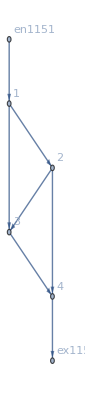

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j418→40,j419→40,j420→0,j421→40,j422→40,j423→80,j424→80,j425→0,j426→0,j427→0,j428→0,j429→0,j430→0,j431→0,jt432→0,jt433→0,jt434→0,jt435→0,jt436→40,jt437→40,jt438→0,jt439→40,jt440→0,jt441→0,jt442→0,jt443→0,jt444→0,jt445→40,jt446→0,jt447→0,jt448→0,jt449→0,jt450→0,jt451→40,jt452→0,jt453→40,jt454→0,jt455→0,u456→96,u457→96,u459→55,u460→55,u461→15,u462→96,u463→56,u464→56,u465→u458,u466→15,u467→15,u468→15,u469→96|>

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

$Aborted

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```